# ACM11 Assignment 3 - Topic 4

## Jacob Snyder

## Part A

```mathematica
(* Definition of a function to be approximated with a fourier series *)
(*f[x_]:=x^2;*)
(*f[x_]:=Exp[x];*)
(*f[x_]:=Sin[x];*)
f[x_]:=Piecewise[{{1,x≤0.5},{-1,x>0.5}}];
```

```mathematica
(* Function definitions of the fourier approximation Fn and its coefficients ak and bk. aks and bks are lists that contain the coefficients ak and bk respectively evaluated at each n 1 through 10 *)
ak[k_]:=2*Integrate[f[x]*Cos[2*k*Pi*x],{x,0,1}];
bk[k_]:=2*Integrate[f[x]*Sin[2*k*Pi*x],{x,0,1}];
aks = Map[ak[#]&,Range[0,10]];
bks = Map[bk[#]&,Range[10]];
Fn[x_,n_]:=aks[[1]]/2+Sum[aks[[k+1]]*Cos[2*k*Pi*x]+bks[[k]]*Sin[2*k*Pi*x],{k,n}];
```

```mathematica
(* Plot the fourier approximation Fn versus the actual function f *)
Manipulate[Plot[{Fn[x,n],f[x]},{x,0,1},PlotLegends->{"Fourier Approximation",f[x]},PlotLabel->"Fourier Approximation vs actual function",AxesLabel->{x,y},PlotRange->Automatic],{n,1,10}]
```

## Part B

```mathematica
(* Define the f_hann function *)
fhann[x_]:=f[x]*1/2*(1-Cos[2*Pi*x]);
```

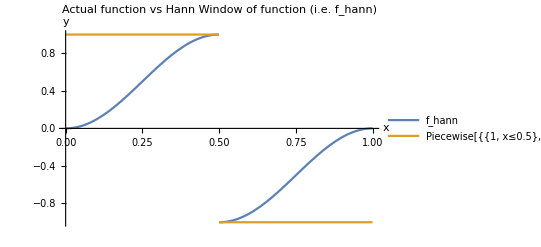

```mathematica
(* Plot the f_hann function versus the original function *)
Plot[{fhann[x],f[x]},{x,0,1},PlotLegends->{"f_hann",f[x]},PlotLabel->"Actual function vs Hann Window of function (i.e. f_hann)",AxesLabel->{x,y},PlotRange->Automatic]
```

```mathematica
(* Definition of the fourier approximation of f_hann, denoted Fhannn and its coefficients ak and bk and ak and bk evaluated at each n 1 through 10 *)
ak[k_]:=2*Integrate[fhann[x]*Cos[2*k*Pi*x],{x,0,1}];
bk[k_]:=2*Integrate[fhann[x]*Sin[2*k*Pi*x],{x,0,1}];
aks = Map[ak[#]&,Range[0,10]];
bks = Map[bk[#]&,Range[10]];
Fhannn[x_,n_]:=aks[[1]]/2+Sum[aks[[k+1]]*Cos[2*k*Pi*x]+bks[[k]]*Sin[2*k*Pi*x],{k,n}];
```

```mathematica
(* Plot f_hann alongside the fourier approximation for f_hann *)
Manipulate[Plot[{Fhannn[x,n],fhann[x]},{x,0,1},PlotLegends->{"Fourier Approximation of f_hann","f_hann"},PlotLabel->"Fourier Approximation of f_hann vs f_hann",AxesLabel->{x,y},PlotRange->Automatic],{n,1,10}]
```

## Part C

```mathematica
(* Define functions eF and ehann that describe the error between f and its fourier approximation, and between f_hann and its fourier approximation respectively *)
eF[n_]:=Integrate[(f[x]-Fn[x,n])^2,{x,0,1}];
ehann[n_]:=Integrate[(fhann[x]-Fhannn[x,n])^2,{x,0,1}];
```

```mathematica
(* Evaluation of the error functions defined above at each n 1 through 10 *)
eFn=Map[eF,Range[10]]
ehannn=Map[ehann,Range[10]]
```

{0.392073,0.482136,0.414589,0.428999,0.404682,0.410637,0.39823,0.401498,0.393993,0.39606}

{0.172358,0.0822944,0.0597785,0.0453684,0.0372627,0.0313075,0.027172,0.0239044,0.0214026,0.019335}

```mathematica
(* Evaluation of the best fit model for the error values calculated just above, following the model B+A/n *)
model1=LinearModelFit[eFn,{1/n},n]
model2=LinearModelFit[ehannn,{1/n},n]
(* From the results below we can see that in the case of e_F(n), A=0.0156671 and B=0.407701, and for e_hann(n),
A=0.168041 and B=0.0027995 *)
(* We therefore conclude that as n->Infinity, e_F(n)->0.407701 and e_hann(n)->0.0027995 *)
```

FittedModel[0.407701+0.0156671/n]

FittedModel[0.0027995+0.168041/n]

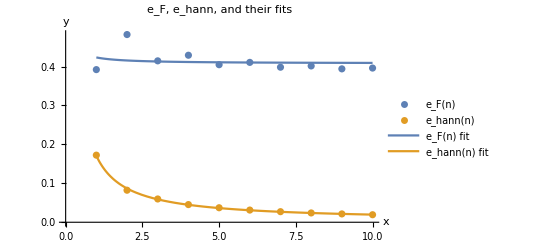

```mathematica
(* Plot of the error values compared to their fitted models *)
Show[ListPlot[{eFn,ehannn},PlotLegends->{"e_F(n)","e_hann(n)"},PlotLabel->"e_F, e_hann, and their fits",AxesLabel->{x,y},PlotRange->Automatic],Plot[{model1[x],model2[x]},{x,1,10},PlotLegends->{"e_F(n) fit","e_hann(n) fit"}]]
```

## Part D

```mathematica
(* Explicit definition of g, as well as ck coefficients for the fourier approximation of the temperature along a bar *)
g[x_]:=Piecewise[{{x,x<5/2},{5-x,x≥5/2}}];
ck[n_]:=2/5*Integrate[g[x]*Sin[n*Pi*x/5],{x,0,5}];
(* Here we calculate the first 30 constants *)ckn=Map[ck,Range[30]];
```

```mathematica
(* Fourier approximation of g *)
gpprox[x_]:=Sum[ckn[[k]]*Sin[k*Pi*x/5],{k,30}];
```

```mathematica
(* Heat equation solution using Mathematica's built in NDSolve solver *)
undsol=NDSolve[{D[und[x,t],t]==D[und[x,t],x,x],und[5,t]==0,und[0,t]==0,und[x,0]==gpprox[x]},und,{x,0,5},{t,0,10}]
```

{{und→InterpolatingFunction[…]}}

```mathematica
(* Definition of fourier approximation to the solution to a heat equation *)
upprox[x_,t_]:=Sum[ckn[[k]]*Sin[k*Pi*x/5]*ⅇ^(-(k*Pi/5)^2*t),{k,30}];
```

```mathematica
(* Plots of both approximations of the solution to the given heat equation as a function of position. Time can be adjusted with the slider. *)
Manipulate[TableForm[{Plot[{N@upprox[x,t]},{x,0,5},PlotLegends->{"NDSolve soln",f[x]},PlotLabel->"NDSolve soln for temperature",AxesLabel->{"Position","Temperature"},PlotRange->{{0,5},{0,2.5}}],Plot[{und[x,t]/.undsol},{x,0,5},PlotLegends->{"Fourier Approximation",f[x]},PlotLabel->"Fourier Approximation of Temperature",AxesLabel->{"Position","Temperature"},PlotRange->{{0,5},{0,2.5}}]}],{t,0,10,0.001}]
```